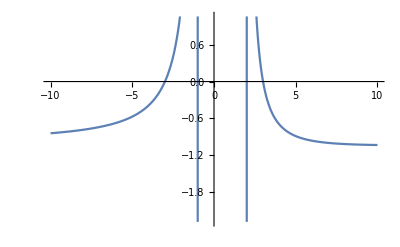

```mathematica
(*dadeno e uravnenieto  (x^2-2x+5)/((x+1)(x-2))-2=0*)
(*1) da se nameri broqt na vsichki koreni i da se lokalizira nay-golemiq i nay-malkiq*)
(*2) napravete 2 iteracii po metoda na nyuton*)
(*3) kakva e tochnostta na poslednata iteraciq*)
(*4) da se nameri lokaliziraniq ot 1) koren s tochnost 10^-14*)
f[x_] := (x^2-2x+5)/((x+1)(x-2))-2;
Plot[f[x],{x,-10,10}]
```

```mathematica
(*uravnenieto ima dva korena*)
```

```mathematica
(*lokalizirane na golemiq koren*)
```

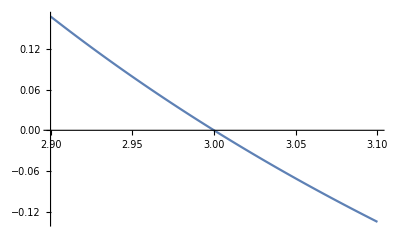

```mathematica
Plot[f[x],{x,2.9,3.1}]
```

```mathematica
f[2.9]
```

0.168091

```mathematica
f[3.1]
```

-0.135255

```mathematica
f[2.9] f[3.1]
```

-0.0227352

```mathematica
(*v izbraniq interval [2.9;3.1] ima koren*)
```

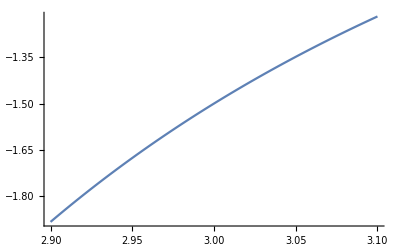

```mathematica
Plot[f'[x],{x,2.9,3.1}]
```

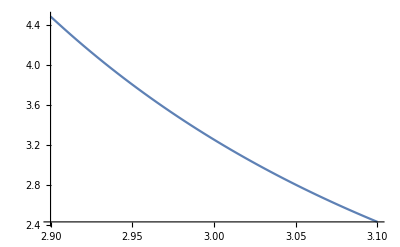

```mathematica
Plot[f''[x],{x,2.9,3.1}]
```

```mathematica
(*purvata proizvodna ima samo otricatelni stoynosti v intervala [2.9;3.1]*)
(*vtorata proizvodna ima samo polojitelni stoynosti v intervala [2.9;3.1]*)
```

```mathematica
(*opredelqma nachalnoto priblijenie (tuk nqma nujda da opredelqme postoqnna tochka)*)
(*tuy kato vtorata proizvodna e polojitelna izbirame tursim takova x0 che f(x0) > 0*)
```

```mathematica
x0 = f[2.9];
Plot[Abs[f''[x]],{x,2.9,3.1}]
```

-Graphics-

```mathematica
(*absolutnata stoynost na vtorata proizvodna dostiga svoq maksimum v leviq kray na intervala *)
```

```mathematica
M2 = Abs[f''[2.9]]
```

4.48256

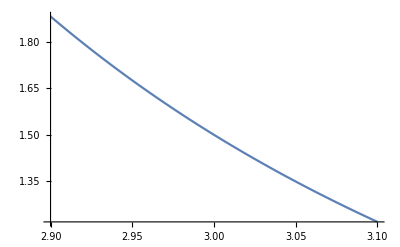

```mathematica
Plot[Abs[f'[x]],{x,2.9,3.1}]
```

```mathematica
(*absolutnata stoynost na purvata proizvodna dostiga svoq minimum v desniq kray na intervala *)
```

```mathematica
m1 = Abs[f'[3.1]]
```

1.21877

```mathematica
K = M2/(2m1)
```

1.83896

```mathematica
(*zapochvame s iteraciite*)
```

```mathematica
x0 = 2.9;
f[x0]
f'[x0]
(*nuleva iteraciq*)
x1 = x0 - f[x0]/f'[x0]
```

0.168091

-1.88229

2.9893

```mathematica
2.9 - 0.16809/-1.882289
```

2.9893

```mathematica
f[x1]
f'[x1]
```

0.0162359

-1.53535

```mathematica
eps1 = K Abs[x1-x0]^2
```

0.0146653

```mathematica
(*vtora iteraciq*)
x = x0;
Print["n=0"," x=",x," f(x)=",f[x]," f'[x]=",f'[x]];
For[n = 1,n<=10,n++,
xnew = x - f[x]/f'[x];
epsn = K(xnew-x)^2;
x = xnew;

Print["n=",n," x=",x," f(x)=",f[x]," f'[x]=",f'[x]," eps=",epsn]
]
```

n=0 x=2.9 f(x)=0.168091 f'[x]=-1.88229

n=1 x=2.9893 f(x)=0.0162359 f'[x]=-1.53535 eps=0.0146653

n=2 x=2.99988 f(x)=0.000185767 f'[x]=-1.5004 eps=0.000205643

n=3 x=3. f(x)=2.49165×10^-8 f'[x]=-1.5 eps=2.81901×10^-8

n=4 x=3. f(x)=8.88178×10^-16 f'[x]=-1.5 eps=5.07415×10^-16

n=5 x=3. f(x)=0. f'[x]=-1.5 eps=3.62672×10^-31

n=6 x=3. f(x)=0. f'[x]=-1.5 eps=0.

n=7 x=3. f(x)=0. f'[x]=-1.5 eps=0.

n=8 x=3. f(x)=0. f'[x]=-1.5 eps=0.

n=9 x=3. f(x)=0. f'[x]=-1.5 eps=0.

n=10 x=3. f(x)=0. f'[x]=-1.5 eps=0.